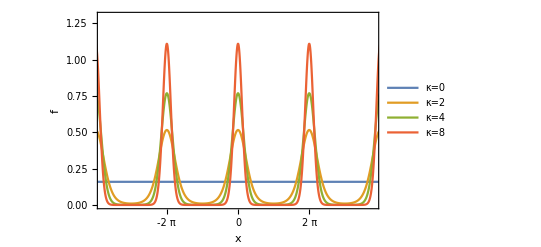

```mathematica
f[x_,κ_,μ_]:= 1/(2 π BesselI[0,κ])ⅇ^(κ Cos[x-μ]);
plot1 = Plot[Evaluate[Table[f[x,κ,0],{κ,{0,2,4,8}}]],{x,-4π,4π},PlotRange->{{-3.8π,3.8π},{0,1.3}},PlotLegends->Placed[Table["κ="<>ToString[κ],{κ,{0,2,4,8}}],{Right,Top}], FrameLabel->{{"f",""},{"x",""}}, Frame->True, FrameTicks->{Range[-4Pi,4Pi,Pi],Automatic}, GridLines->{Range[-4Pi,2Pi,Pi],Automatic}];
Show[plot1]
Export[NotebookDirectory[]<>"../Plots/VMM.png",plot1,"PNG"];
Export[NotebookDirectory[]<>"../Plots/VMM.svg",plot1,"SVG"];
```